## Bang-bang control of harmonic oscillator (Problem 7.16)

```mathematica
Clear["Global`*"];
SetOptions[Plot,PlotRange -> All,ExclusionsStyle->Dashed,PlotStyle->Thick];
T=2π (* end time *);
```

```mathematica
u=Piecewise[{{-1,0<t<π},{1,π<t<2π}}];
eq1=x''[t]+x[t]==u;  (* 2nd-order step response *)
initCond1= {x[0]==0,x'[0]==0};
xs =DSolveValue[{eq1,initCond1},x[t],t]
```

Piecewise[{{0, t≤0}, {-1+Cos[t], 0<t≤π}, {1+3 Cos[t], π<t≤2 π}, {4 Cos[t], True}}]

```mathematica
xsdot=D[xs, t]//Simplify
```

Piecewise[{{-4 Sin[t], t>2 π}, {-3 Sin[t], π<t<2 π}, {-Sin[t], 0<t<π}, {0, True}}]

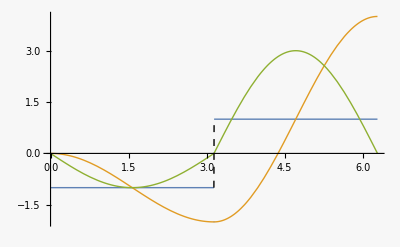

```mathematica
solPlot1=Plot[{u,xs,xsdot},{t,0,T}]
```

```mathematica
f0=Integrate[Abs[Sin[τ-T]],{τ,0,t},Assumptions ->0<t<2π]
```

Piecewise[{{2, t==π||t≥2 π||t≤0}, {1-Cos[t], 0<t<π}, {3+Cos[t], True}}]

The function f0(t) isn' t really necessary, but ....

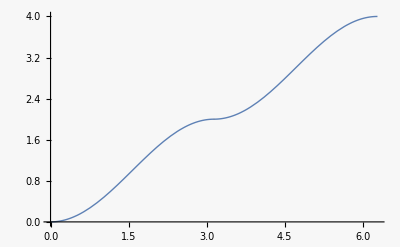

```mathematica
Plot[Piecewise[{{2,t==π||t≥2 π||t≤0},{1-Cos[t],0<t<π}},3+Cos[t]],{t,0,2π}]
```

```mathematica
cost2go=f0-xs Cos[t-T]+xsdot Sin[t-T] //Simplify
```

Piecewise[{{2, t≤0}, {-2, t≥2 π}, {0, True}}]

Another approach:  Calculate cost function vs. switching time numerically and maximize directly.

```mathematica
J[τ0_,τ_]:=Module[{u,t,x,eq,init,xs},
u=-1+2UnitStep[t-τ0];
eq=x''[t]+x[t]==u;  (* 2nd-order step response *)
init= {x[0]==0,x'[0]==0};
xs =NDSolveValue[{eq,init},x,{t,0,τ}];xs[τ]]
```

```mathematica
J[π,2π]  (* confirm that the maximum value is, in fact, J=4 *)
```

4.

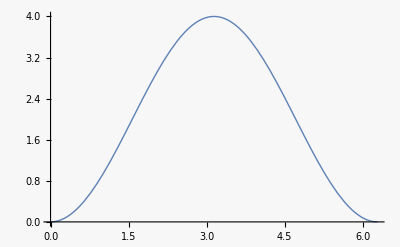

```mathematica
Plot[J[t,2π],{t,0,2π}]
```

We can also the same calculation analytically:

```mathematica
u=-1;
eq={x1'[t]==x2[t],x2'[t]==-x1[t]+u};  (* 2nd-order step response *)
init= {x1[0]==0,x2[0]==0};
DSolveValue[{eq,init},{x1[t],x2[t]},t]//Simplify
```

{-1+Cos[t],-Sin[t]}

```mathematica
u=1;
eq={x1'[t]==x2[t],x2'[t]==-x1[t]+u};  (* 2nd-order step response *)
init= {x1[τ0]==-1+Cos[τ0],x2[τ0]==-Sin[τ0]};
DSolveValue[{eq,init},{x1[t],x2[t]},t]//Simplify
```

{1+Cos[t]-2 Cos[t-τ0],-Sin[t]+2 Sin[t-τ0]}

```mathematica
J=1+Cos[τ]-2 Cos[τ-τ0];D[J, τ0]
```

-2 Sin[τ-τ0]

```mathematica
Plot[J/.τ->2π,{τ0,0,2π}]
```

-Graphics-